-7.5242×10^10+2.57713×10^12 x-4.18831×10^13 x^2+4.29994×10^14 x^3-3.13218×10^15 x^4+1.72357×10^16 x^5-7.44836×10^16 x^6+2.59412×10^17 x^7-7.4143×10^17 x^8+1.76156×10^18 x^9-3.51121×10^18 x^10+5.90894×10^18 x^11-8.42983×10^18 x^12+1.0216×10^19 x^13-1.05192×10^19 x^14+9.18762×10^18 x^15-6.78205×10^18 x^16+4.20603×10^18 x^17-2.17233×10^18 x^18+9.22789×10^17 x^19-3.16758×10^17 x^20+8.56503×10^16 x^21-1.75563×10^16 x^22+2.56319×10^15 x^23-2.37415×10^14 x^24+1.04833×10^13 x^25

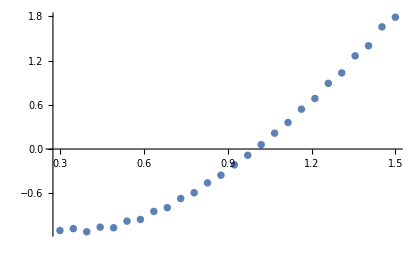

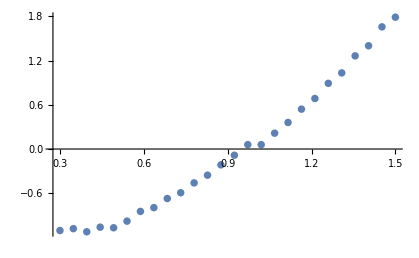

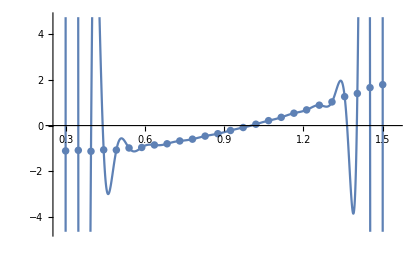

```mathematica
arr1={0.3, 0.348,0.396,0.444, 0.492, 0.54, 0.588, 0.636, 0.684, 0.732,0.78, 0.828, 0.876, 0.924, 0.972, 1.02,1.068,1.116,1.164,1.212,1.26,1.308,1.356,1.404,1.452,1.5};
arr2={-1.10525, -1.07996, -1.1225,-1.05986,-1.06783,-0.978257,-0.955469,-0.846209,-0.794931,-0.671395,-0.593028,-0.459459,-0.354877,-0.214726,-0.0844691,0.0593841,0.215,0.360097,0.540909,0.685119,0.891074,1.03252,1.26364,1.40065,1.65703,1.7881};
h=0.048;
n=Length[arr1];funk={};
For[i=1,i≤n,i++,funk=Append[funk,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk];
inpln:=InterpolatingPolynomial[funk,x];Collect[inpln,x]
ListPlot[funk]
gr1:=Plot[inpln,{x,0.252,1.548}];
gr2:=ListPlot[funk];
data = {{0.3,-1.10525},{0.348,-1.07996},{0.396,-1.1225},{0.444,-1.05986},{0.492,-1.06783},{0.54,-0.978257},{0.588,-0.846209},{0.636,-0.794931},{0.684,-0.671395},{0.732,-0.593028},{0.78,-0.459459},{0.828,-0.354877},{0.876,-0.214726},{0.924,-0.0844691},{0.972,0.0593841},
{1.02,0.0593841},{1.068,0.215},{1.116,0.360097},{1.164,0.540909},{1.212,0.685119},{1.26,0.891074},{1.308,1.03252},{1.356,1.26364},
{1.404,1.40065},{1.452,1.65703},{1.5,1.7881}};
ListPlot[data]


Show[{gr1,gr2}]
```